# Radioactive decay calculations: Analytical and numerical solution of Bateman’s system of differential equations

Time constants (T^(-1), time in minutes) and system matrix.

```mathematica
λ1 = 0.000126
λ2 = 0.2237
λ3 = 0.02586
λ4 = 0.03482
λ5 =  70.4333
λ6 = 0.0000000645
λ7 = 0.000096
λ8 = 0.0002087

A=({{-λ1, 0, 0, 0, 0, 0, 0, 0}, {λ1, -λ2, 0, 0, 0, 0, 0, 0}, {0, λ2, -λ3, 0, 0, 0, 0, 0}, {0, 0, λ3, -λ4, 0, 0, 0, 0}, {0, 0, 0, λ4, -λ5, 0, 0, 0}, {0, 0, 0, 0, λ5, -λ6, 0, 0}, {0, 0, 0, 0, 0, λ6, -λ7, 0}, {0, 0, 0, 0, 0, 0, λ7, -λ8}})
```

0.000126

0.2237

0.02586

0.03482

70.4333

6.45×10^-8

0.000096

0.0002087

{{-0.000126,0,0,0,0,0,0,0},{0.000126,-0.2237,0,0,0,0,0,0},{0,0.2237,-0.02586,0,0,0,0,0},{0,0,0.02586,-0.03482,0,0,0,0},{0,0,0,0.03482,-70.4333,0,0,0},{0,0,0,0,70.4333,-6.45×10^-8,0,0},{0,0,0,0,0,6.45×10^-8,-0.000096,0},{0,0,0,0,0,0,0.000096,-0.0002087}}

```mathematica
Eigenvalues[A]
```

{-70.4333,-0.2237,-0.03482,-0.02586,-0.0002087,-0.000126,-0.000096,-6.45×10^-8}

Column vector of unknowns as functions of time.

```mathematica
X[t_]={Rn222[t],Po218[t],Pb214[t],Bi214[t],Po214[t],Pb210[t],Bi210[t],Po210[t]};
```

Solution of Bateman system in symbolic form.

```mathematica
system = X'[t]==A.X[t];
sol=DSolve[system,{Rn222,Po218,Pb214,Bi214,Po214,Pb210,Bi210,Po210},t]
```

{{Bi210→Function[{t},ⅇ^(-70.7181 t) (-6.77914×10^-29 ⅇ^(0.284811 t)-1.64273×10^-27 ⅇ^(70.4944 t)+9.6108×10^-22 ⅇ^(70.6833 t)-2.83108×10^-21 ⅇ^(70.6923 t)+6.2707×10^-17 ⅇ^(70.7179 t)+9.07395×10^-19 ⅇ^(70.718 t)+1. ⅇ^(70.718 t)+6.94546×10^-17 ⅇ^(70.7181 t)) C[1]+0.000672328 ⅇ^(-70.7181 t) (-6.737×10^-10 ⅇ^(0.284811 t)-9.43665×10^-21 ⅇ^(70.4944 t)+0.00276417 ⅇ^(70.6833 t)-2.57975×10^-16 ⅇ^(70.6923 t)-2.90081×10^-17 ⅇ^(70.7179 t)-5.30778×10^-12 ⅇ^(70.718 t)-1.00276 ⅇ^(70.718 t)+1. ⅇ^(70.7181 t)) C[2]+0.000672327 ⅇ^(-70.7181 t) (1.4428×10^-22 ⅇ^(0.284811 t)-9.22242×10^-21 ⅇ^(70.4944 t)+9.20291×10^-17 ⅇ^(70.6833 t)-2.57635×10^-16 ⅇ^(70.6923 t)-2.88342×10^-17 ⅇ^(70.7179 t)-5.30787×10^-12 ⅇ^(70.718 t)-1. ⅇ^(70.718 t)+1. ⅇ^(70.7181 t)) C[3]+0.00067233 ⅇ^(-70.7181 t) (2.47443×10^-13 ⅇ^(0.284811 t)+3.91687×10^-21 ⅇ^(70.4944 t)-0.00797781 ⅇ^(70.6833 t)+0.0144759 ⅇ^(70.6923 t)-2.9244×10^-17 ⅇ^(70.7179 t)-5.30888×10^-12 ⅇ^(70.718 t)-1.0065 ⅇ^(70.718 t)+1. ⅇ^(70.7181 t)) C[4]+ⅇ^(-70.7181 t) (7.94759×10^-29 ⅇ^(0.284811 t)+7.95102×10^-28 ⅇ^(70.4944 t)-7.32898×10^-22 ⅇ^(70.6833 t)+2.60269×10^-21 ⅇ^(70.6923 t)-7.36154×10^-17 ⅇ^(70.7179 t)-4.39187×10^-19 ⅇ^(70.718 t)+1.55444×10^-16 ⅇ^(70.718 t)-8.13916×10^-17 ⅇ^(70.7181 t)) C[5]+0.000672327 ⅇ^(-70.7181 t) (1.36208×10^-6 ⅇ^(0.284811 t)-9.69499×10^-21 ⅇ^(70.4944 t)+9.24514×10^-17 ⅇ^(70.6833 t)-2.58368×10^-16 ⅇ^(70.6923 t)-2.88342×10^-17 ⅇ^(70.7179 t)-5.30772×10^-12 ⅇ^(70.718 t)-1. ⅇ^(70.718 t)+1. ⅇ^(70.7181 t)) C[6]+0.00067233 ⅇ^(-70.7181 t) (-7.88399×10^-16 ⅇ^(0.284811 t)+0.0000103714 ⅇ^(70.4944 t)-0.00944852 ⅇ^(70.6833 t)+0.0163681 ⅇ^(70.6923 t)-2.92713×10^-17 ⅇ^(70.7179 t)-5.30902×10^-12 ⅇ^(70.718 t)-1.00693 ⅇ^(70.718 t)+1. ⅇ^(70.7181 t)) C[7]+0.000672674 ⅇ^(-70.7181 t) (1.79305×10^-21 ⅇ^(0.284811 t)-5.84203×10^-9 ⅇ^(70.4944 t)+0.0000342971 ⅇ^(70.6833 t)-0.000080101 ⅇ^(70.6923 t)+4.45743×10^-17 ⅇ^(70.7179 t)+3.22699 ⅇ^(70.718 t)-4.22694 ⅇ^(70.718 t)+1. ⅇ^(70.7181 t)) C[8]],Bi214→Function[{t},ⅇ^(-70.718 t) (-1.13506×10^-38 ⅇ^(0.284715 t)-3.64704×10^-20 ⅇ^(70.4943 t)+5.17147×10^-16 ⅇ^(70.6832 t)-8.39546×10^-16 ⅇ^(70.6922 t)+3.20909×10^-16 ⅇ^(70.7178 t)+1.52643×10^-18 ⅇ^(70.7179 t)+2.51222×10^-27 ⅇ^(70.718 t)) C[1]+ⅇ^(-70.718 t) (-7.58387×10^-23 ⅇ^(0.284715 t)-1.40856×10^-16 ⅇ^(70.4943 t)+1. ⅇ^(70.6832 t)-5.14342×10^-14 ⅇ^(70.6922 t)-9.9808×10^-20 ⅇ^(70.7178 t)-6.00308×10^-15 ⅇ^(70.7179 t)+2.43185×10^-14 ⅇ^(70.718 t)) C[2]+ⅇ^(-70.718 t) (1.62417×10^-35 ⅇ^(0.284715 t)-1.37658×10^-16 ⅇ^(70.4943 t)+3.32935×10^-14 ⅇ^(70.6832 t)-5.13663×10^-14 ⅇ^(70.6922 t)-9.92095×10^-20 ⅇ^(70.7178 t)-6.00317×10^-15 ⅇ^(70.7179 t)+2.43185×10^-14 ⅇ^(70.718 t)) C[3]+ⅇ^(-70.718 t) (2.78548×10^-26 ⅇ^(0.284715 t)+5.84651×10^-17 ⅇ^(70.4943 t)-2.88616 ⅇ^(70.6832 t)+2.88616 ⅇ^(70.6922 t)-1.0062×10^-19 ⅇ^(70.7178 t)-6.00434×10^-15 ⅇ^(70.7179 t)+2.43186×10^-14 ⅇ^(70.718 t)) C[4]+ⅇ^(-70.718 t) (1.3307×10^-38 ⅇ^(0.284715 t)+1.76522×10^-20 ⅇ^(70.4943 t)-3.94365×10^-16 ⅇ^(70.6832 t)+7.7182×10^-16 ⅇ^(70.6922 t)-3.76734×10^-16 ⅇ^(70.7178 t)-7.38804×10^-19 ⅇ^(70.7179 t)-2.94399×10^-27 ⅇ^(70.718 t)) C[5]+ⅇ^(-70.718 t) (1.53329×10^-19 ⅇ^(0.284715 t)-1.44712×10^-16 ⅇ^(70.4943 t)+3.34463×10^-14 ⅇ^(70.6832 t)-5.15123×10^-14 ⅇ^(70.6922 t)-9.92098×10^-20 ⅇ^(70.7178 t)-6.003×10^-15 ⅇ^(70.7179 t)+2.43185×10^-14 ⅇ^(70.718 t)) C[6]+ⅇ^(-70.718 t) (-8.87507×10^-29 ⅇ^(0.284715 t)+0.154808 ⅇ^(70.4943 t)-3.41822 ⅇ^(70.6832 t)+3.26342 ⅇ^(70.6922 t)-1.00714×10^-19 ⅇ^(70.7178 t)-6.00451×10^-15 ⅇ^(70.7179 t)+2.43186×10^-14 ⅇ^(70.718 t)) C[7]+ⅇ^(-70.718 t) (2.01948×10^-34 ⅇ^(0.284715 t)-0.0000872456 ⅇ^(70.4943 t)+0.0124141 ⅇ^(70.6832 t)-0.0159785 ⅇ^(70.6922 t)+1.53446×10^-19 ⅇ^(70.7178 t)+0.00365159 ⅇ^(70.7179 t)+2.43311×10^-14 ⅇ^(70.718 t)) C[8]],Pb210→Function[{t},ⅇ^(-70.718 t) (7.40274×10^-20 ⅇ^(0.284715 t)+5.69489×10^-21 ⅇ^(70.4943 t)-5.17404×10^-16 ⅇ^(70.6832 t)+1.13085×10^-15 ⅇ^(70.6922 t)-1.03496×10^-13 ⅇ^(70.7178 t)-4.22044×10^-16 ⅇ^(70.7179 t)+1.03305×10^-13 ⅇ^(70.718 t)) C[1]+1. ⅇ^(-70.718 t) (0.000494612 ⅇ^(0.284715 t)+2.19947×10^-17 ⅇ^(70.4943 t)-1.00049 ⅇ^(70.6832 t)+6.92807×10^-14 ⅇ^(70.6922 t)+3.2189×10^-17 ⅇ^(70.7178 t)+1.6598×10^-12 ⅇ^(70.7179 t)+1. ⅇ^(70.718 t)) C[2]+1. ⅇ^(-70.718 t) (-1.05927×10^-16 ⅇ^(0.284715 t)+2.14954×10^-17 ⅇ^(70.4943 t)-3.33101×10^-14 ⅇ^(70.6832 t)+6.91893×10^-14 ⅇ^(70.6922 t)+3.19961×10^-17 ⅇ^(70.7178 t)+1.65983×10^-12 ⅇ^(70.7179 t)+1. ⅇ^(70.718 t)) C[3]+1. ⅇ^(-70.718 t) (-1.81666×10^-7 ⅇ^(0.284715 t)-9.12934×10^-18 ⅇ^(70.4943 t)+2.88758 ⅇ^(70.6832 t)-3.88758 ⅇ^(70.6922 t)+3.24509×10^-17 ⅇ^(70.7178 t)+1.66014×10^-12 ⅇ^(70.7179 t)+1. ⅇ^(70.718 t)) C[4]+ⅇ^(-70.718 t) (-8.67868×10^-20 ⅇ^(0.284715 t)-2.7564×10^-21 ⅇ^(70.4943 t)+3.9456×10^-16 ⅇ^(70.6832 t)-1.03962×10^-15 ⅇ^(70.6922 t)+1.215×10^-13 ⅇ^(70.7178 t)+2.04273×10^-16 ⅇ^(70.7179 t)-1.2106×10^-13 ⅇ^(70.718 t)) C[5]+1. ⅇ^(-70.718 t) (-1. ⅇ^(0.284715 t)+2.25968×10^-17 ⅇ^(70.4943 t)-3.34629×10^-14 ⅇ^(70.6832 t)+6.9386×10^-14 ⅇ^(70.6922 t)+3.19962×10^-17 ⅇ^(70.7178 t)+1.65978×10^-12 ⅇ^(70.7179 t)+1. ⅇ^(70.718 t)) C[6]+1. ⅇ^(-70.718 t) (5.78821×10^-10 ⅇ^(0.284715 t)-0.0241734 ⅇ^(70.4943 t)+3.41991 ⅇ^(70.6832 t)-4.39573 ⅇ^(70.6922 t)+3.24811×10^-17 ⅇ^(70.7178 t)+1.66019×10^-12 ⅇ^(70.7179 t)+1. ⅇ^(70.718 t)) C[7]+1.00052 ⅇ^(-70.718 t) (-1.31641×10^-15 ⅇ^(0.284715 t)+0.0000136164 ⅇ^(70.4943 t)-0.0124139 ⅇ^(70.6832 t)+0.0215116 ⅇ^(70.6922 t)-4.94623×10^-17 ⅇ^(70.7178 t)-1.00911 ⅇ^(70.7179 t)+1. ⅇ^(70.718 t)) C[8]],Pb214→Function[{t},ⅇ^(-70.7181 t) (8.51991×10^-38 ⅇ^(0.284811 t)+2.66378×10^-19 ⅇ^(70.4944 t)+3.80709×10^-38 ⅇ^(70.6833 t)-2.90887×10^-16 ⅇ^(70.6923 t)+2.2684×10^-16 ⅇ^(70.7179 t)+2.04787×10^-18 ⅇ^(70.718 t)+6.17325×10^-17 ⅇ^(70.718 t)+2.55599×10^-27 ⅇ^(70.7181 t)) C[1]+ⅇ^(-70.7181 t) (5.69257×10^-22 ⅇ^(0.284811 t)+1.0288×10^-15 ⅇ^(70.4944 t)+7.36171×10^-23 ⅇ^(70.6833 t)-1.7821×10^-14 ⅇ^(70.6923 t)-7.0551×10^-20 ⅇ^(70.7179 t)-8.05378×10^-15 ⅇ^(70.718 t)-4.16192×10^-20 ⅇ^(70.718 t)+2.47422×10^-14 ⅇ^(70.7181 t)) C[2]+ⅇ^(-70.7181 t) (-1.21912×10^-34 ⅇ^(0.284811 t)+1.00544×10^-15 ⅇ^(70.4944 t)+2.45097×10^-36 ⅇ^(70.6833 t)-1.77974×10^-14 ⅇ^(70.6923 t)-7.0128×10^-20 ⅇ^(70.7179 t)-8.05391×10^-15 ⅇ^(70.718 t)-4.15044×10^-20 ⅇ^(70.718 t)+2.47422×10^-14 ⅇ^(70.7181 t)) C[3]+ⅇ^(-70.7181 t) (-2.09083×10^-25 ⅇ^(0.284811 t)-4.27026×10^-16 ⅇ^(70.4944 t)-2.12471×10^-22 ⅇ^(70.6833 t)+1. ⅇ^(70.6923 t)-7.1125×10^-20 ⅇ^(70.7179 t)-8.05547×10^-15 ⅇ^(70.718 t)-4.17743×10^-20 ⅇ^(70.718 t)+2.47423×10^-14 ⅇ^(70.7181 t)) C[4]+ⅇ^(-70.7181 t) (-9.9884×10^-38 ⅇ^(0.284811 t)-1.28931×10^-19 ⅇ^(70.4944 t)-2.9032×10^-38 ⅇ^(70.6833 t)+2.67421×10^-16 ⅇ^(70.6923 t)-2.66301×10^-16 ⅇ^(70.7179 t)-9.91186×10^-19 ⅇ^(70.718 t)+9.59597×10^-33 ⅇ^(70.718 t)-2.99527×10^-27 ⅇ^(70.7181 t)) C[5]+ⅇ^(-70.7181 t) (-1.15091×10^-18 ⅇ^(0.284811 t)+1.05697×10^-15 ⅇ^(70.4944 t)+2.46222×10^-36 ⅇ^(70.6833 t)-1.78481×10^-14 ⅇ^(70.6923 t)-7.01282×10^-20 ⅇ^(70.7179 t)-8.05368×10^-15 ⅇ^(70.718 t)-4.15045×10^-20 ⅇ^(70.718 t)+2.47422×10^-14 ⅇ^(70.7181 t)) C[6]+ⅇ^(-70.7181 t) (6.66176×10^-28 ⅇ^(0.284811 t)-1.13071 ⅇ^(70.4944 t)-2.5164×10^-22 ⅇ^(70.6833 t)+1.13071 ⅇ^(70.6923 t)-7.11914×10^-20 ⅇ^(70.7179 t)-8.0557×10^-15 ⅇ^(70.718 t)-4.17922×10^-20 ⅇ^(70.718 t)+2.47423×10^-14 ⅇ^(70.7181 t)) C[7]+ⅇ^(-70.7181 t) (-1.51585×10^-33 ⅇ^(0.284811 t)+0.000637237 ⅇ^(70.4944 t)+9.13893×10^-25 ⅇ^(70.6833 t)-0.00553624 ⅇ^(70.6923 t)+1.08466×10^-19 ⅇ^(70.7179 t)+0.00489901 ⅇ^(70.718 t)-1.75527×10^-19 ⅇ^(70.718 t)+2.47549×10^-14 ⅇ^(70.7181 t)) C[8]],Po210→Function[{t},ⅇ^(-70.7181 t) (9.23922×10^-35 ⅇ^(0.284811 t)+7.0563×10^-31 ⅇ^(70.4944 t)-2.66571×10^-24 ⅇ^(70.6833 t)+1.05953×10^-23 ⅇ^(70.6923 t)-0.851819 ⅇ^(70.7179 t)+1.05332×10^-18 ⅇ^(70.718 t)+0.851819 ⅇ^(70.718 t)+3.19583×10^-17 ⅇ^(70.7181 t)) C[1]+0.00030936 ⅇ^(-70.7181 t) (1.99547×10^-15 ⅇ^(0.284811 t)+8.8094×10^-24 ⅇ^(70.4944 t)-0.0000166623 ⅇ^(70.6833 t)+2.09825×10^-18 ⅇ^(70.6923 t)+0.85638 ⅇ^(70.7179 t)-1.33905×10^-11 ⅇ^(70.718 t)-1.85636 ⅇ^(70.718 t)+1. ⅇ^(70.7181 t)) C[2]+0.000309359 ⅇ^(-70.7181 t) (-4.27351×10^-28 ⅇ^(0.284811 t)+8.6094×10^-24 ⅇ^(70.4944 t)-5.54748×10^-19 ⅇ^(70.6833 t)+2.09548×10^-18 ⅇ^(70.6923 t)+0.851247 ⅇ^(70.7179 t)-1.33907×10^-11 ⅇ^(70.718 t)-1.85125 ⅇ^(70.718 t)+1. ⅇ^(70.7181 t)) C[3]+0.000309361 ⅇ^(-70.7181 t) (-7.32915×10^-19 ⅇ^(0.284811 t)-3.65652×10^-24 ⅇ^(70.4944 t)+0.0000480899 ⅇ^(70.6833 t)-0.00011774 ⅇ^(70.6923 t)+0.863346 ⅇ^(70.7179 t)-1.33932×10^-11 ⅇ^(70.718 t)-1.86328 ⅇ^(70.718 t)+1. ⅇ^(70.7181 t)) C[4]+ⅇ^(-70.7181 t) (-1.08317×10^-34 ⅇ^(0.284811 t)-3.41534×10^-31 ⅇ^(70.4944 t)+2.03281×10^-24 ⅇ^(70.6833 t)-9.74058×10^-24 ⅇ^(70.6923 t)+1. ⅇ^(70.7179 t)-5.09817×10^-19 ⅇ^(70.718 t)+1.3241×10^-16 ⅇ^(70.718 t)-3.74509×10^-17 ⅇ^(70.7181 t)) C[5]+0.000309359 ⅇ^(-70.7181 t) (-4.03441×10^-12 ⅇ^(0.284811 t)+9.05056×10^-24 ⅇ^(70.4944 t)-5.57293×10^-19 ⅇ^(70.6833 t)+2.10144×10^-18 ⅇ^(70.6923 t)+0.851249 ⅇ^(70.7179 t)-1.33903×10^-11 ⅇ^(70.718 t)-1.85125 ⅇ^(70.718 t)+1. ⅇ^(70.7181 t)) C[6]+0.000309361 ⅇ^(-70.7181 t) (2.3352×10^-21 ⅇ^(0.284811 t)-9.682×10^-9 ⅇ^(70.4944 t)+0.0000569553 ⅇ^(70.6833 t)-0.00013313 ⅇ^(70.6923 t)+0.864152 ⅇ^(70.7179 t)-1.33936×10^-11 ⅇ^(70.718 t)-1.86408 ⅇ^(70.718 t)+1. ⅇ^(70.7181 t)) C[7]+0.000309519 ⅇ^(-70.7181 t) (-5.31092×10^-27 ⅇ^(0.284811 t)+5.45371×10^-12 ⅇ^(70.4944 t)-2.06742×10^-7 ⅇ^(70.6833 t)+6.51504×10^-7 ⅇ^(70.6923 t)-1.31593 ⅇ^(70.7179 t)+8.14104 ⅇ^(70.718 t)-7.82511 ⅇ^(70.718 t)+1. ⅇ^(70.7181 t)) C[8]],Po214→Function[{t},ⅇ^(-70.7181 t) (-7.40274×10^-20 ⅇ^(0.284811 t)-1.80873×10^-23 ⅇ^(70.4944 t)+2.55788×10^-19 ⅇ^(70.6833 t)-4.15197×10^-19 ⅇ^(70.6923 t)+2.32611×10^-19 ⅇ^(70.7179 t)+7.54619×10^-22 ⅇ^(70.718 t)+8.95336×10^-23 ⅇ^(70.718 t)) C[1]+ⅇ^(-70.7181 t) (-0.000494613 ⅇ^(0.284811 t)-6.98565×10^-20 ⅇ^(70.4944 t)+0.000494613 ⅇ^(70.6833 t)-2.54368×10^-17 ⅇ^(70.6923 t)-7.23459×10^-23 ⅇ^(70.7179 t)-2.96774×10^-18 ⅇ^(70.718 t)-6.03624×10^-26 ⅇ^(70.718 t)) C[2]+ⅇ^(-70.7181 t) (1.05927×10^-16 ⅇ^(0.284811 t)-6.82704×10^-20 ⅇ^(70.4944 t)+1.64674×10^-17 ⅇ^(70.6833 t)-2.54032×10^-17 ⅇ^(70.6923 t)-7.19121×10^-23 ⅇ^(70.7179 t)-2.96779×10^-18 ⅇ^(70.718 t)-6.01959×10^-26 ⅇ^(70.718 t)) C[3]+ⅇ^(-70.7181 t) (1.81667×10^-7 ⅇ^(0.284811 t)+2.89954×10^-20 ⅇ^(70.4944 t)-0.00142753 ⅇ^(70.6833 t)+0.00142735 ⅇ^(70.6923 t)-7.29345×10^-23 ⅇ^(70.7179 t)-2.96836×10^-18 ⅇ^(70.718 t)-6.05873×10^-26 ⅇ^(70.718 t)) C[4]+ⅇ^(-70.7181 t) (8.67868×10^-20 ⅇ^(0.284811 t)+8.75448×10^-24 ⅇ^(70.4944 t)-1.95058×10^-19 ⅇ^(70.6833 t)+3.81703×10^-19 ⅇ^(70.6923 t)-2.73076×10^-19 ⅇ^(70.7179 t)-3.65242×10^-22 ⅇ^(70.718 t)+1.39175×10^-38 ⅇ^(70.718 t)) C[5]+ⅇ^(-70.7181 t) (1. ⅇ^(0.284811 t)-7.17688×10^-20 ⅇ^(70.4944 t)+1.6543×10^-17 ⅇ^(70.6833 t)-2.54754×10^-17 ⅇ^(70.6923 t)-7.19123×10^-23 ⅇ^(70.7179 t)-2.9677×10^-18 ⅇ^(70.718 t)-6.01959×10^-26 ⅇ^(70.718 t)) C[6]+ⅇ^(-70.7181 t) (-5.78824×10^-10 ⅇ^(0.284811 t)+0.0000767762 ⅇ^(70.4944 t)-0.0016907 ⅇ^(70.6833 t)+0.00161392 ⅇ^(70.6923 t)-7.30026×10^-23 ⅇ^(70.7179 t)-2.96844×10^-18 ⅇ^(70.718 t)-6.06133×10^-26 ⅇ^(70.718 t)) C[7]+ⅇ^(-70.7181 t) (1.31709×10^-15 ⅇ^(0.284811 t)-4.32689×10^-8 ⅇ^(70.4944 t)+6.1402×10^-6 ⅇ^(70.6833 t)-7.90216×10^-6 ⅇ^(70.6923 t)+1.11225×10^-22 ⅇ^(70.7179 t)+1.80523×10^-6 ⅇ^(70.718 t)-2.54576×10^-25 ⅇ^(70.718 t)) C[8]],Po218→Function[{t},ⅇ^(-70.7181 t) (-3.37109×10^-36 ⅇ^(0.284811 t)-2.35584×10^-19 ⅇ^(70.4944 t)+1.06855×10^-32 ⅇ^(70.6833 t)+3.43322×10^-31 ⅇ^(70.6923 t)+1.66914×10^-24 ⅇ^(70.7179 t)+2.35583×10^-19 ⅇ^(70.718 t)+2.5723×10^-31 ⅇ^(70.718 t)+1.94976×10^-28 ⅇ^(70.7181 t)) C[1]+ⅇ^(-70.7181 t) (-2.25239×10^-20 ⅇ^(0.284811 t)-9.09872×10^-16 ⅇ^(70.4944 t)+2.06624×10^-17 ⅇ^(70.6833 t)+2.10334×10^-29 ⅇ^(70.6923 t)-5.1913×10^-28 ⅇ^(70.7179 t)-9.26491×10^-16 ⅇ^(70.718 t)-1.73421×10^-34 ⅇ^(70.718 t)+1.88738×10^-15 ⅇ^(70.7181 t)) C[2]+ⅇ^(-70.7181 t) (4.82373×10^-33 ⅇ^(0.284811 t)-8.89213×10^-16 ⅇ^(70.4944 t)+6.87923×10^-31 ⅇ^(70.6833 t)+2.10056×10^-29 ⅇ^(70.6923 t)-5.16016×10^-28 ⅇ^(70.7179 t)-9.26506×10^-16 ⅇ^(70.718 t)-1.72943×10^-34 ⅇ^(70.718 t)+1.88738×10^-15 ⅇ^(70.7181 t)) C[3]+ⅇ^(-70.7181 t) (8.27282×10^-24 ⅇ^(0.284811 t)+3.77661×10^-16 ⅇ^(70.4944 t)-5.96349×10^-17 ⅇ^(70.6833 t)-1.18026×10^-15 ⅇ^(70.6923 t)-5.23353×10^-28 ⅇ^(70.7179 t)-9.26685×10^-16 ⅇ^(70.718 t)-1.74067×10^-34 ⅇ^(70.718 t)+1.88739×10^-15 ⅇ^(70.7181 t)) C[4]+ⅇ^(-70.7181 t) (3.95213×10^-36 ⅇ^(0.284811 t)+1.14026×10^-19 ⅇ^(70.4944 t)-8.1485×10^-33 ⅇ^(70.6833 t)-3.15626×10^-31 ⅇ^(70.6923 t)-1.9595×10^-24 ⅇ^(70.7179 t)-1.14024×10^-19 ⅇ^(70.718 t)+3.99849×10^-47 ⅇ^(70.718 t)-2.28485×10^-28 ⅇ^(70.7181 t)) C[5]+ⅇ^(-70.7181 t) (4.55384×10^-17 ⅇ^(0.284811 t)-9.34779×10^-16 ⅇ^(70.4944 t)+6.91079×10^-31 ⅇ^(70.6833 t)+2.10653×10^-29 ⅇ^(70.6923 t)-5.16018×10^-28 ⅇ^(70.7179 t)-9.26479×10^-16 ⅇ^(70.718 t)-1.72943×10^-34 ⅇ^(70.718 t)+1.88738×10^-15 ⅇ^(70.7181 t)) C[6]+ⅇ^(-70.7181 t) (-2.63587×10^-26 ⅇ^(0.284811 t)+1. ⅇ^(70.4944 t)-7.06285×10^-17 ⅇ^(70.6833 t)-1.33453×10^-15 ⅇ^(70.6923 t)-5.23842×10^-28 ⅇ^(70.7179 t)-9.26711×10^-16 ⅇ^(70.718 t)-1.74142×10^-34 ⅇ^(70.718 t)+1.88739×10^-15 ⅇ^(70.7181 t)) C[7]+ⅇ^(-70.7181 t) (5.99781×10^-32 ⅇ^(0.284811 t)-0.000563572 ⅇ^(70.4944 t)+2.56505×10^-19 ⅇ^(70.6833 t)+6.53421×10^-18 ⅇ^(70.6923 t)+7.98115×10^-28 ⅇ^(70.7179 t)+0.000563572 ⅇ^(70.718 t)-7.31396×10^-34 ⅇ^(70.718 t)+1.88836×10^-15 ⅇ^(70.7181 t)) C[8]],Rn222→Function[{t},ⅇ^(-70.4944 t) (3.50555×10^-36 ⅇ^(0.0611108 t)-1.53468×10^-32 ⅇ^(70.4596 t)-6.56892×10^-32 ⅇ^(70.4686 t)-1.72343×10^-16 ⅇ^(70.4942 t)+4.18017×10^-16 ⅇ^(70.4943 t)-2.45674×10^-16 ⅇ^(70.4943 t)+1.69824×10^-25 ⅇ^(70.4944 t)) C[1]+1.64391×10^-12 ⅇ^(-70.4944 t) (1.42479×10^-8 ⅇ^(0.0611108 t)-0.000018052 ⅇ^(70.4596 t)-2.44807×10^-18 ⅇ^(70.4686 t)+3.26062×10^-8 ⅇ^(70.4942 t)-1.00003 ⅇ^(70.4943 t)+1.00754×10^-7 ⅇ^(70.4943 t)+1. ⅇ^(70.4944 t)) C[2]+1.64391×10^-12 ⅇ^(-70.4944 t) (-3.05135×10^-21 ⅇ^(0.0611108 t)-6.01015×10^-19 ⅇ^(70.4596 t)-2.44484×10^-18 ⅇ^(70.4686 t)+3.24107×10^-8 ⅇ^(70.4942 t)-1.00005 ⅇ^(70.4943 t)+1.00476×10^-7 ⅇ^(70.4943 t)+1. ⅇ^(70.4944 t)) C[3]+1.64391×10^-12 ⅇ^(-70.4944 t) (-5.23312×10^-12 ⅇ^(0.0611108 t)+0.0000521007 ⅇ^(70.4596 t)+0.00013737 ⅇ^(70.4686 t)+3.28714×10^-8 ⅇ^(70.4942 t)-1.00024 ⅇ^(70.4943 t)+1.01129×10^-7 ⅇ^(70.4943 t)+1. ⅇ^(70.4944 t)) C[4]+ⅇ^(-70.4944 t) (-4.10977×10^-36 ⅇ^(0.0611108 t)+1.17031×10^-32 ⅇ^(70.4596 t)+6.039×10^-32 ⅇ^(70.4686 t)+2.02324×10^-16 ⅇ^(70.4942 t)-2.02324×10^-16 ⅇ^(70.4943 t)-3.81886×10^-32 ⅇ^(70.4943 t)-1.99011×10^-25 ⅇ^(70.4944 t)) C[5]+1.64391×10^-12 ⅇ^(-70.4944 t) (-0.0000288063 ⅇ^(0.0611108 t)-6.03772×10^-19 ⅇ^(70.4596 t)-2.45179×10^-18 ⅇ^(70.4686 t)+3.24108×10^-8 ⅇ^(70.4942 t)-1.00002 ⅇ^(70.4943 t)+1.00476×10^-7 ⅇ^(70.4943 t)+1. ⅇ^(70.4944 t)) C[6]+1.64392×10^-12 ⅇ^(-70.4944 t) (1.66737×10^-14 ⅇ^(0.0611108 t)+0.0000617055 ⅇ^(70.4596 t)+0.000155325 ⅇ^(70.4686 t)+3.29021×10^-8 ⅇ^(70.4942 t)-1.00027 ⅇ^(70.4943 t)+1.01172×10^-7 ⅇ^(70.4943 t)+1. ⅇ^(70.4944 t)) C[7]+1.64476×10^-12 ⅇ^(-70.4944 t) (-3.79207×10^-20 ⅇ^(0.0611108 t)-2.23984×10^-7 ⅇ^(70.4596 t)-7.60122×10^-7 ⅇ^(70.4686 t)-5.01032×10^-8 ⅇ^(70.4942 t)+6.07992×10^11 ⅇ^(70.4943 t)+4.24706×10^-7 ⅇ^(70.4943 t)+1. ⅇ^(70.4944 t)) C[8]]}}

Numerical solution of of Bateman system over the time interval 0 to 4x(10^9) min. What are the units below?
The units for the initial conditions are in number of atoms because Bateman equations measure the decay in atoms as a function of time for a decay chain. The plots are of a function of time in seconds.

```mathematica
s = NDSolve [{X'[t] == A.X[t], {Rn222[0] ==2269149.149
, Po218[0] ==0, Pb214[0] ==0,Bi214[0] ==0,Po214[0] ==0,Pb210[0] ==0,Bi210[0] ==0,Po210[0] ==0}}, {Rn222,Po218,Pb214,Bi214,Po214,Pb210,Bi210,Po210}, {t, 0, 4000000000}]
```

{{Rn222→InterpolatingFunction[…],Po218→InterpolatingFunction[…],Pb214→InterpolatingFunction[…],Bi214→InterpolatingFunction[…],Po214→InterpolatingFunction[…],Pb210→InterpolatingFunction[…],Bi210→InterpolatingFunction[…],Po210→InterpolatingFunction[…]}}

The Plot below is all the Radionuclides in picograms as a function of time.

```mathematica
Plot[{(Rn222[t] / 2707692307692310000000.00)*10^12/.s,  
(Po218[t] / 2763231197771590000000.00)*10^12/.s, 
(Pb214[t]/ 2810457516339870000000.00)*10^12/.s, 
(Bi214 [t] / 2818584070796460000000.00)*10^12/.s,
(Po214[t] / 2819354838709680000000.00)*10^12/.s, 
(Pb210[t] / 2864661654135340000000.00)*10^12/.s, 
(Bi210[t] / 2867132867132870000000.00)*10^12/.s, 
(Po210[t] / 2863741339491920000000.00)*10^12/.s}, {t, 0, 18000},PlotLabels->"Expressions", PlotRange->{{0, 18000},{0, .0002}}]
```

-Graphics-

The  Plot below is number of atoms as a function of time.

```mathematica
Plot[{(Rn222[t] * λ1)/.s}, {t, 0, 18000},PlotLabels->"Expressions", PlotRange->{{0, 5616},{0, 400}}]
```

-Graphics-

Same graph as above except that we use a logarithmic-scale ordinate. It separates the various graphs.

```mathematica
LogPlot[{(Rn222[t])/.s,  (Po218[t])/.s, (Pb214[t])/.s, (Bi214 [t])/.s,(Po214[t])/.s, (Pb210[t])/.s, (Bi210[t])/.s, (Po210[t])/.s}, {t, 0, 18000},PlotLabels->"Expressions", PlotRange->{{0, 18000},{10^-8, 10000000}}]
```

-Graphics-

Same graph as above except that we use a logarithmic scale for both axes. Since zero cannot be included in the time scale, we start the time at 10^-6 min. I prefer the previous display.

```mathematica
LogLogPlot[{(Rn222[t])/.s,  (Po218[t])/.s, (Pb214[t])/.s, (Bi214 [t])/.s,(Po214[t])/.s, (Pb210[t])/.s, (Bi210[t])/.s, (Po210[t])/.s}, {t, 10^-6, 18000},PlotLabels->"Expressions", PlotRange->{{10^-6, 18000},{10^-50, 10^7}}]
```

-Graphics-

The plot below is the activity of the radionuclides as a function of time on two different timescales.
Activity for 5 hours:

```mathematica
Plot[{(Rn222[t] * λ1)/.s,  (Po218[t]*λ2)/.s, (Pb214[t] * λ3)/.s, (Bi214 [t]* λ4)/.s,(Po214[t] * λ5)/.s, (Pb210[t] * λ6)/.s, (Bi210[t] * λ7)/.s, (Po210[t]* λ8)/.s}, {t, 0, 18000},PlotLabels->"Expressions", PlotRange->{{0, 18000},{0, 1000}}]
```

-Graphics-

LogPlot of above.

```mathematica
LogPlot[{(Rn222[t] * λ1)/.s,  (Po218[t]*λ2)/.s, (Pb214[t] * λ3)/.s, (Bi214 [t]* λ4)/.s,(Po214[t] * λ5)/.s, (Pb210[t] * λ6)/.s, (Bi210[t] * λ7)/.s, (Po210[t]* λ8)/.s}, {t, 0, 18000},PlotLabels->"Expressions", PlotRange->{{0, 18000},{10^-10, 10^4}}]
```

-Graphics-

Activity just over 2 days:

```mathematica
Plot[{(Pb210[t] * λ6)/.s, (Bi210[t] * λ7)/.s, (Po210[t]* λ8)/.s}, {t, 0, 180000},PlotLabels->"Expressions", PlotRange->{{0, 180000},{0, .5}}]
```

-Graphics-

The plot below is the gross alpha produced by Radon-222  for initial condition’s amount.

```mathematica
Plot[{(Rn222[t] * λ1 +Po218[t]*λ2 + Po214[t] * λ5 + Po210[t]* λ8)/.s}, {t, 0, 18000},PlotLabels->"Expressions", PlotRange->{{0, 18000},{0, 3000}}]
```

-Graphics-

The plot below is the gross beta produced by Radon-222 for the initial condition’s amount.

```mathematica
Plot[{(Pb214[t] * λ3+Bi214 [t]* λ4+Pb210[t] * λ6+Bi210[t] * λ7)/.s}, {t, 0, 18000},PlotLabels->"Expressions", PlotRange->{{0, 18000},{0, 2000}}]
```

-Graphics-

The plot below is the total gross alpha and gross beta activity combined produced by Radon-222 for the initial condition’s amount.

```mathematica
Plot[{(Rn222[t] * λ1 +Po218[t]*λ2 + Po214[t] * λ5 + Po210[t]* λ8 + Pb214[t] * λ3+Bi214 [t]* λ4+Pb210[t] * λ6+Bi210[t] * λ7)/.s}, {t, 0, 300},PlotLabels->"Expressions", PlotRange->{{0, 300},{0, 1500}}]
```

-Graphics-

Alpha Activity when adding a liter of atoms every 12 hours (timescale in minutes)

```mathematica
stepPlot[t_] :=∑_(n=0)^11 UnitStep[t-720*n] * (Rn222[t-720*n]* λ1+Po218[t-720*n]*λ2 + Po214[t-720*n] * λ5 
+ Po210[t-720*n]* λ8)/.s
```

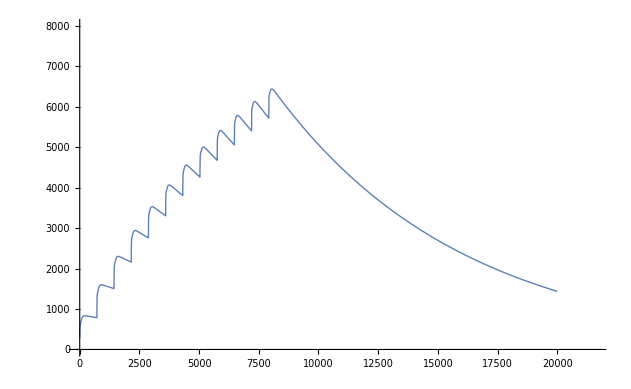

```mathematica
Plot[∑_(n=0)^11 UnitStep[t-720*n] * (Rn222[t-720*n]* λ1+Po218[t-720*n]*λ2 + Po214[t-720*n] * λ5 
+ Po210[t-720*n]* λ8)/.s,{t,-0,20000},PlotStyle->Thick,  
PlotRange->{{0, 21600},{0, 8000}}]
```

```mathematica
step = Table[stepPlot[t], {t, 0, 21600,1}]
```

{{285.913},{343.191},{389.024},{425.753},{455.246},{478.996},{498.193},{513.785},{526.53},{537.029},{545.762},{553.112},{559.38},{564.807},{569.584},{573.862},{577.758},{581.367},{584.761},{587.999},{591.124},{594.171},21557,{1178.03},{1177.88},{1177.73},{1177.58},{1177.44},{1177.29},{1177.14},{1176.99},{1176.84},{1176.7},{1176.55},{1176.4},{1176.25},{1176.1},{1175.96},{1175.81},{1175.66},{1175.51},{1175.36},{1175.22},{1175.07},{1174.92}}
 |  |  |  |

```mathematica
Export["stepFunction.xls", step]

SystemOpen["stepFunction.xls"]
```

stepFunction.xls

Radiation Energy in Joules from Alpha Emitters

```mathematica
Plot[{(1.6*10^-13*(Rn222[t] * 5.5+Po218[t]*6.0+ Po214[t] *7.7+ Po210[t]* 5.3))/.s,(Rn222[t] * 5.5*1.6*10^-13)/.s, (Po218[t]*6.0*1.6*10^-13)/.s, (Po214[t] *7.7*1.6*10^-13)/.s,( Po210[t]* 5.3*1.6*10^-13)/.s}, {t, 0, 4300},PlotLabels->"Expressions", PlotRange->{{0, 4300},{0, .00000001}}]
```

Part::take: Cannot take positions 1 through 4 in {112,138,146}.

-Graphics-

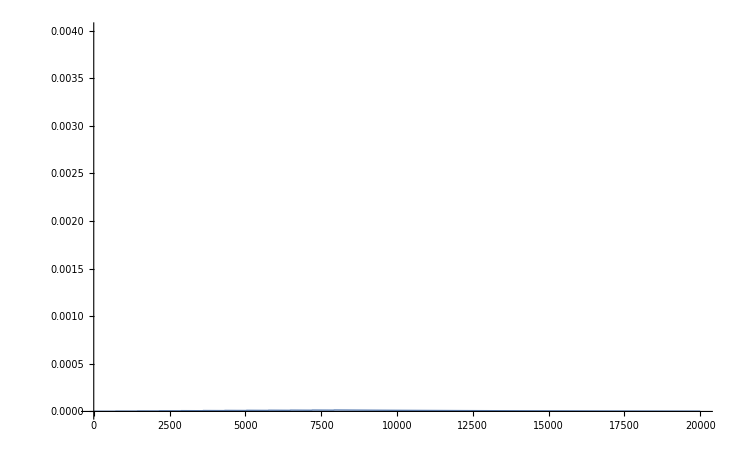

```mathematica
Plot[{∑_(n=0)^11 UnitStep[t-720*n]*(1.6*10^-13*(Rn222[t-720*n] * 5.5+Po218[t-720*n]*6.0+ Po214[t-720*n] *7.7+ Po210[t-720*n]* 5.3))/.s}, {t,-0,20000},PlotStyle->Thick,  PlotRange->{{0, 20000},{0, .004}}]
```

```mathematica
Remove[s]
s = NDSolve [{X'[t] == A.X[t], {Rn222[0] ==229029.029
, Po218[0] ==0, Pb214[0] ==0,Bi214[0] ==0,Po214[0] ==0,Pb210[0] ==0,Bi210[0] ==0,Po210[0] ==0}}, {Rn222,Po218,Pb214,Bi214,Po214,Pb210,Bi210,Po210}, {t, 0, 4000000000}]
```

{{Rn222→InterpolatingFunction[…],Po218→InterpolatingFunction[…],Pb214→InterpolatingFunction[…],Bi214→InterpolatingFunction[…],Po214→InterpolatingFunction[…],Pb210→InterpolatingFunction[…],Bi210→InterpolatingFunction[…],Po210→InterpolatingFunction[…]}}

Report of Statewide Surveillance for Radon in Selected Community Water Systems Executive Summary Sample Minium Alpha Activity when adding a liter of atoms every 12 hours (timescale in minutes)

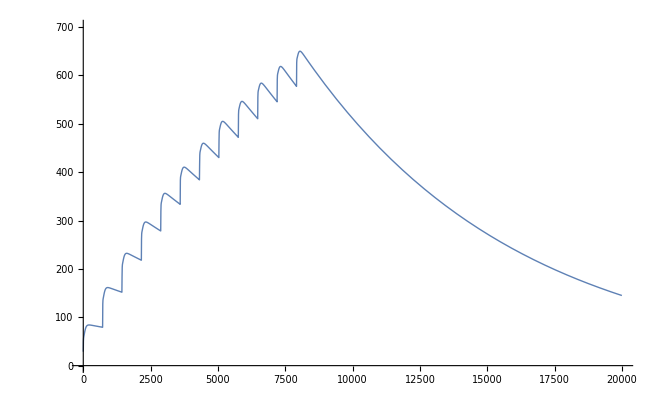

```mathematica
Plot[∑_(n=0)^11 UnitStep[t-720*n] * (Rn222[t-720*n]* λ1+Po218[t-720*n]*λ2 + Po214[t-720*n] * λ5 + Po210[t-720*n]* λ8)/.s,{t,-0,20000},PlotStyle->Thick,  PlotRange->{{0, 20000},{0, 700}}]
```

Radiation Energy in Joules from Alpha Emitters from Report of Statewide Surveillance for Radon in Selected Community Water Systems Executive Summary Sample Minium Alpha Activity

```mathematica
Plot[{((Rn222[t] * 5.5+Po218[t]*6.0+ Po214[t] *7.7+ Po210[t]* 5.3)*1.6*10^-13)/.s,(Rn222[t] * 5.5*1.6*10^-13)/.s, (Po218[t]*6.0*1.6*10^-13)/.s, (Po214[t] *7.7*1.6*10^-13)/.s,( Po210[t]* 5.3*1.6*10^-13)/.s}, {t, 0, 43200},PlotLabels->"Expressions", PlotRange->{{0, 43200},{0, .0000000002}}]
```

Part::take: Cannot take positions 1 through 4 in {87,76,173}.

-Graphics-

```mathematica
s = NDSolve [{X'[t] == A.X[t], {Rn222[0] ==472152152.2
, Po218[0] ==0, Pb214[0] ==0,Bi214[0] ==0,Po214[0] ==0,Pb210[0] ==0,Bi210[0] ==0,Po210[0] ==0}}, {Rn222,Po218,Pb214,Bi214,Po214,Pb210,Bi210,Po210}, {t, 0, 4000000000}]
```

{{Rn222→InterpolatingFunction[…],Po218→InterpolatingFunction[…],Pb214→InterpolatingFunction[…],Bi214→InterpolatingFunction[…],Po214→InterpolatingFunction[…],Pb210→InterpolatingFunction[…],Bi210→InterpolatingFunction[…],Po210→InterpolatingFunction[…]}}

Report of Statewide Surveillance for Radon in Selected Community Water Systems Executive Summary Sample Maximum Alpha Activity when adding a liter of atoms every 12 hours (timescale in minutes)

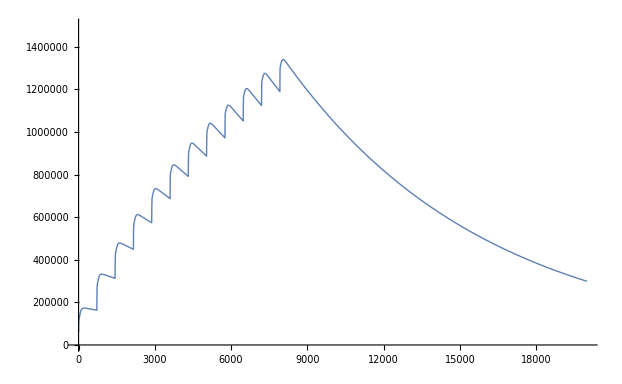

```mathematica
Plot[∑_(n=0)^11 UnitStep[t-720*n] * (Rn222[t-720*n]* λ1+Po218[t-720*n]*λ2 + Po214[t-720*n] * λ5 + Po210[t-720*n]* λ8)/.s,{t,-0,20000},PlotStyle->Thick,  PlotRange->{{0, 20000},{0, 1500000}}]
```

Radiation Energy in Joules from Alpha Emitters from Report of Statewide Surveillance for Radon in Selected Community Water Systems Executive Summary Sample Maximum Alpha Activity

```mathematica
Plot[{((Rn222[t] * 5.5+Po218[t]*6.0+ Po214[t] *7.7+ Po210[t]* 5.3)*1.6*10^-13)/.s,(Rn222[t] * 5.5*1.6*10^-13)/.s, (Po218[t]*6.0*1.6*10^-13)/.s, (Po214[t] *7.7*1.6*10^-13)/.s,( Po210[t]* 5.3*1.6*10^-13)/.s}, {t, 0, 43200},PlotLabels->"Expressions", PlotRange->{{0, 43200},{0, .0000003}}]
```

Part::take: Cannot take positions 1 through 4 in {98,110,203}.

-Graphics-